## 1.1 Imperfect transcritical bifurcation

### a)

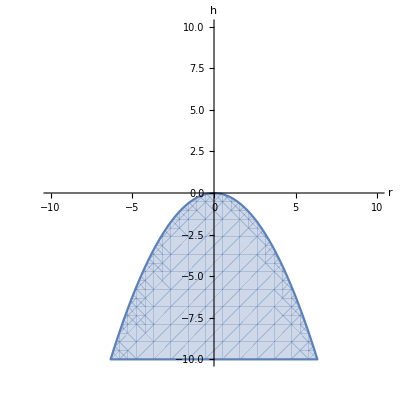

```mathematica
Clear["Global`*"]
RegionPlot[h<-r^2/4,{r,-10,10},{h,-10,10},
AxesLabel->Automatic,
Axes->True,
Frame->None,
FrameLabel->{r,h},
RotateLabel->False,
LabelStyle->(FontSize->12)]
```

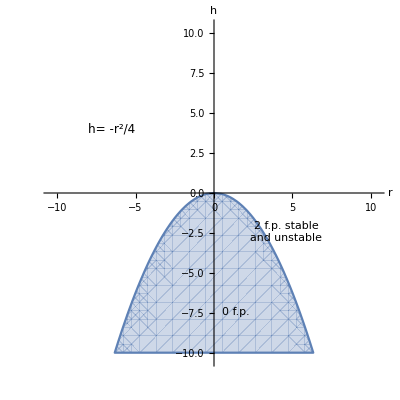

### b)

```mathematica
Clear["Global`*"]
x1 = (r+√(r^2+4*h))/2;
x2 = (r-√(r^2+4*h))/2;
Show[
Plot3D[x1,{r,-10,10},{h,-10,10},
AxesOrigin->{0,0,0},
PlotRange->{-11,11}],
Plot3D[x2,{r,-10,10},{h,-10,10},
AxesOrigin->{0,0,0},
PlotRange->{-11,11}],
Graphics3D[{Text["r",{10,0,0}],
Text["h",{0,10,0}],
Text["x^*",{0,0,11}]}],
Boxed->False]
```

-Graphics3D-